# Mathematics on the computer PH2140

Instructors: 
Prabha Mandayam (prabhamd@physics.iitm.ac.in)
Arul Lakshminarayan (arul@physics.iitm.ac.in)

We expect to have 12 classes, each with an Assignment.

The assignments must preferably be done by the end of the class. However, they can be submitted on the last working day before the next class.

Please refer to the handouts (uploaded on Moodle) for Grading Scheme, Topics, and Textbooks.

```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
2+3
```

5

```mathematica
2+3;
```

```mathematica
a=1
```

1

```mathematica
a:=1
```

```mathematica
a=1;
```

```mathematica
a+4
```

5

```mathematica
Pi
```

π

```mathematica
N[Pi]
```

3.14159

```mathematica
Cos[Pi]
```

-1

```mathematica
x^n-x^2/.n->3
```

```mathematica
-x^2+(x^3)^□
```

```mathematica
f[var_,A_,B_]:=A((var-B)^2)^□
```

```mathematica
f[x,1,0]
```

x^2

```mathematica
f[2,1,0]
```

4

### Plot: Basic tools, Visualization, Multiple plots.

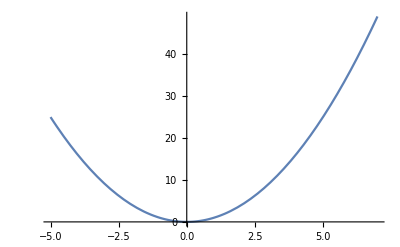

```mathematica
Plot[f[x,1,0],{x,-5,7}]
```

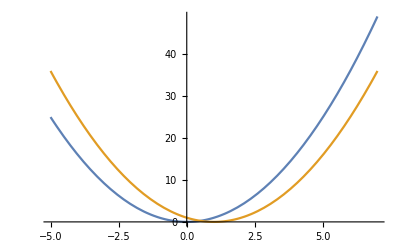

```mathematica
Plot[{f[x,1,0],f[x,1,1]},{x,-5,7}]
```

```mathematica
D[f[x,A,B],x]
```

2 A (-B+x)

```mathematica
D[f[x,A,B],x,x]
```

2 A

```mathematica
D[f[x,A,B],x,x]/((1+(D[f[x,A,B],x])^2)^(3/2))
```

(2 A)/((1+4 A^2 (-B+x)^2)^(3/2))

```mathematica
κ[x_,A_,B_]:=(2 A)/((1+4 A^2 (-B+x)^2)^(3/2))
```

```mathematica
(*CHECK: The definition below does NOT work*)
κ[x_,A_,B_]:=D[f[x,A,B],x,x]/((1+(D[f[x,A,B],x])^2)^(3/2))
```

```mathematica
κ[x,1,0]
```

2/((1+4 x^2)^(3/2))

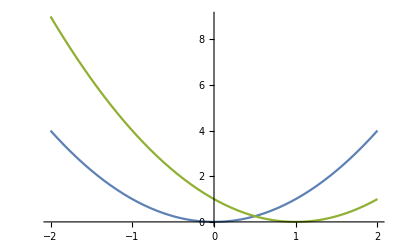

```mathematica
Plot[{f[x,1,0],κ[x,1,0],f[x,1,1],κ[x,1,1]},{x,-2,2}]
```

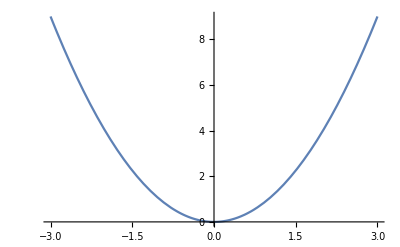
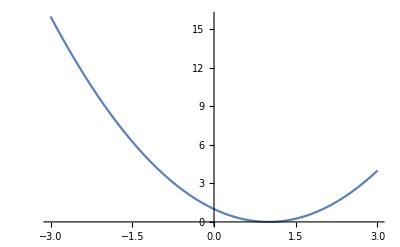
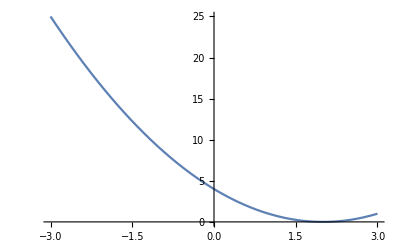

```mathematica
Evaluate@Table[Plot[{f[x,1,B],κ[x,1,B]},{x,-3,3}],{B,0,2,1}]
```

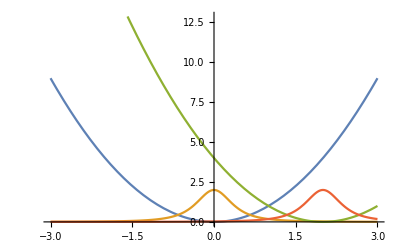

```mathematica
Plot[Evaluate@Table[{f[x,1,B],κ[x,1,B]},{B,0,2,2}],{x,-3,3}]
```

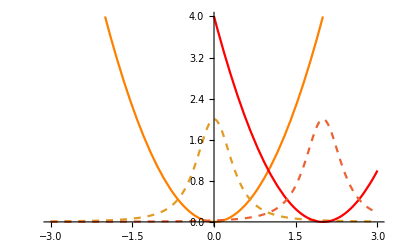

```mathematica
Plot[Evaluate@Table[{f[x,1,B],κ[x,1,B]},{B,0,2,2}],{x,-3,3},PlotRange->{0,4},PlotStyle->{Orange,Dashed,Red,Dashed}]
```

### Parametric Plot:

```mathematica
g:=9.8
```

```mathematica
X[t_,α_]:=Cos[α]t
```

```mathematica
Y[t_,α_]:=Sin[α]t-1/2 g t^2
```

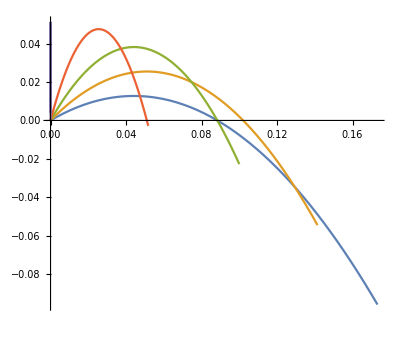

```mathematica
exp1=ParametricPlot[Evaluate@Table[{X[t,s],Y[t,s]},{s,Pi/6,(Pi/2),Pi/12}],{t,0,.2},PlotRange->All]
```

```mathematica
Export["/Users/dawoodkothawala/Dropbox/ph2140/sample-plot.pdf",exp1];
```

```mathematica
p1:=Table[ParametricPlot[{X[t,s],Y[t,s]},{t,0,2Sin[s]/g},PlotRange->All],{s,Pi/6,(Pi/2),Pi/12}]
```

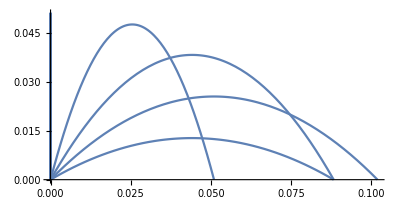

```mathematica
Show[p1]
```

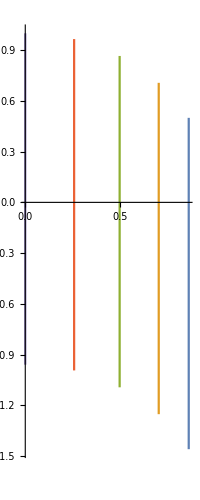

```mathematica
ParametricPlot[Evaluate@Table[{D[X[t,s],t],D[Y[t,s],t]},{s,Pi/6,(Pi/2),Pi/12}],{t,0,.2},PlotRange->All]
```

```mathematica
g:=1
```

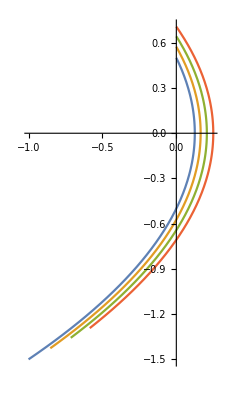

```mathematica
ParametricPlot[Evaluate@Table[{Y[t,s],D[Y[t,s],t]},{s,(30/180)Pi,(45/180)Pi,(5/180)Pi}],{t,0,2}]
```